```mathematica
link=Install[LinkConnect["34799@192.168.150.128,38359@192.168.150.128",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,Ωhe=1/4,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θbp=0.045,θbhe=0.0225,ωbp=15*Sqrt[0.45],ωbhe=7.5*Sqrt[0.45],ωe=150,
ωp ={0.039893,0.143882,0.348679,0.597894,0.815419,0.984766,1.11653,1.21888,1.29599,1.34998,1.38201,1.39263,1.38201,1.34998,1.29599,1.21888,1.11653,0.984766,0.815419,0.597894,0.348679,0.143882,0.039893},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd,vr]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe,Ωhe},{ωbp,ωe,ωbhe},{θbp,θe,θbhe}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
check=With[{k=4.0,wna=87Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.9,0.03] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

```mathematica
sol=With[{k=Range[2.0,5.0,0.05],wna=87Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.44,0.029] (1+0.0001 I {0,1,2}),MaxIterations->100]];
ListLinePlot[Im[sol[[2,2]]]]
```

```mathematica
gama={};
with[{k=Range[17]},gama=Append[gama,Im[sol[[2,2,k]]]]];
Export["2.txt",gama];
```

{2.65572+0.0093115 ⅈ,2.67995+0.0266231 ⅈ,2.67992+0.0266363 ⅈ,2.69538+0.0305515 ⅈ,2.71257+0.031572 ⅈ,2.73153+0.0299508 ⅈ,2.75255+0.0259509 ⅈ,2.77617+0.0199904 ⅈ,2.80306+0.0129218 ⅈ,2.83356+0.00636114 ⅈ}

{2.65572+0.0093115 ⅈ,2.67995+0.0266231 ⅈ,2.67992+0.0266363 ⅈ,2.69538+0.0305515 ⅈ,2.71257+0.031572 ⅈ,2.73153+0.0299508 ⅈ,2.75255+0.0259509 ⅈ,2.77617+0.0199904 ⅈ,2.80306+0.0129218 ⅈ,2.83356+0.00636114 ⅈ,2.8666+0.0021958 ⅈ,2.89998+0.000916897 ⅈ,2.93214+0.00149157 ⅈ,2.96214+0.00265851 ⅈ,2.98622-0.000443647 ⅈ,3.02934+0.00471045 ⅈ,3.05629+0.00643966 ⅈ,3.08401+0.00720154 ⅈ,3.11139+0.00735484 ⅈ,3.13816+0.00665832 ⅈ,3.16425+0.00465892 ⅈ,3.18979+0.000751057 ⅈ,3.21505-0.00586439 ⅈ,3.24041-0.0164584 ⅈ,3.26585-0.0337052 ⅈ,3.28628-0.0610567 ⅈ,3.28628-0.0610567 ⅈ,3.44157-0.00184487 ⅈ,3.4622+0.0107805 ⅈ,3.48282+0.0190495 ⅈ,3.50347+0.0241928 ⅈ,3.54352+0.0271273 ⅈ,3.54538+0.0275395 ⅈ}

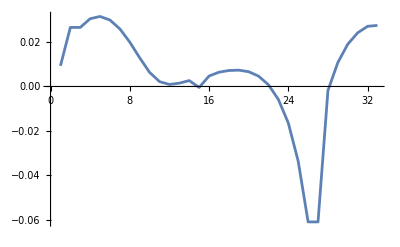

```mathematica
sol1=With[{k=Range[3.95,3.5,-0.05],wna=86Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.77,0.02] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol2=With[{k=Range[4.0,5.1,0.05],wna=86Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.77,0.02] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol1=Reverse[sol1[[2,2]]]
sol=Join[sol1,sol2[[2,2]]]
ListLinePlot[Im[sol]]
```

```mathematica
Export["heim86.csv",Im[sol]];

Export["here87.csv",Re[sol]];
```